## New Silhouette Functions

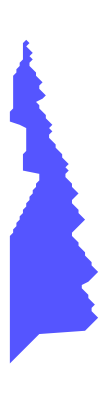

```mathematica
ShowSilhouette[ru, "Opacity"->1]
```

### Overlaying different perturbations

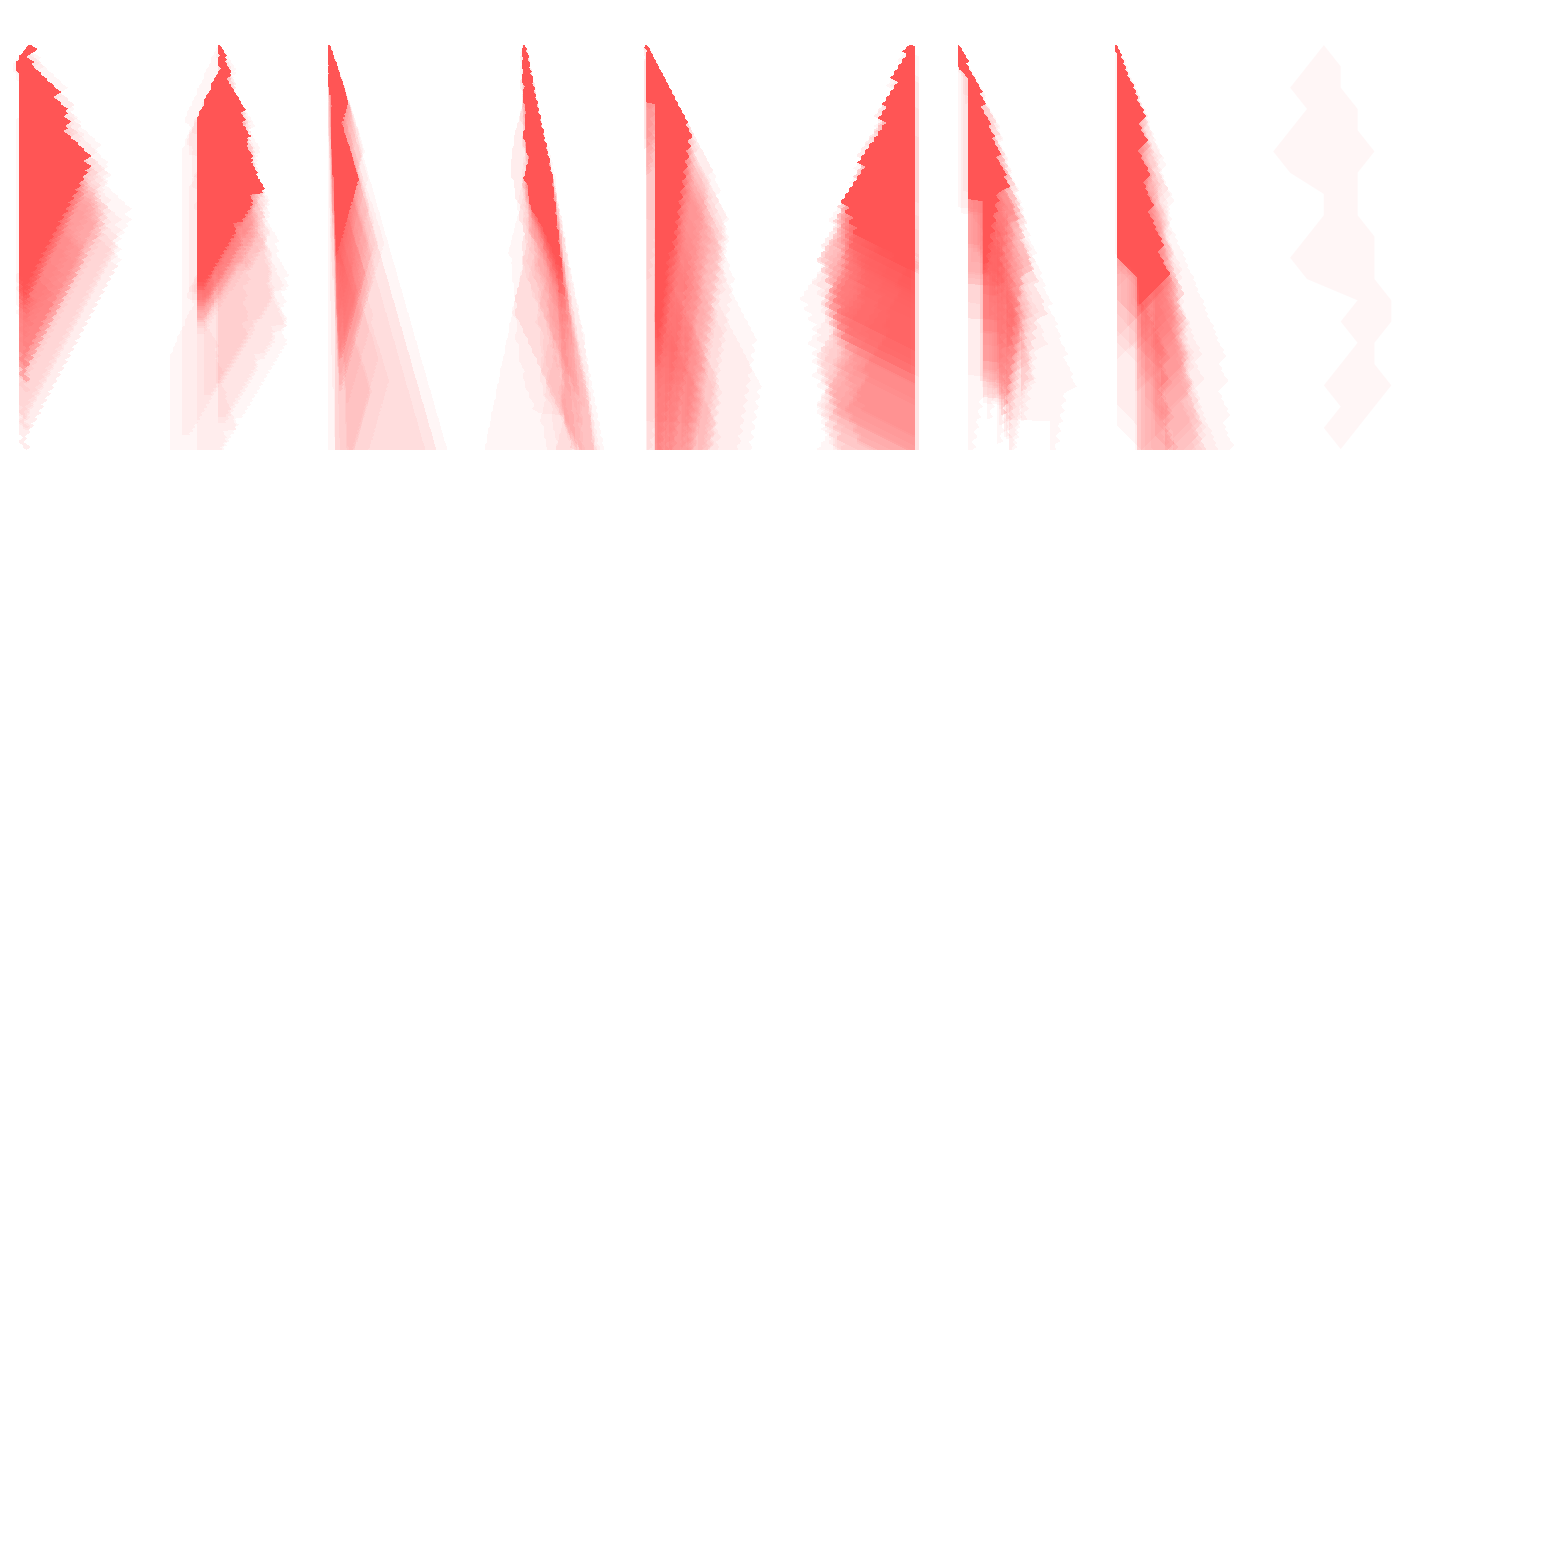

```mathematica
Show@@Table[PlotSilhouette[#, "Perturbation"->1, "Opacity"->0.05, "Color"->Lighter[Red]], {i, 100}]&/@ cands
```